# remove interaction start in n=0 only

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
um=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
cm=10^-2;
ms=10^-3;
ωrCs=2π 150kHz;
ωaCs=2π 25kHz;
ωrNa=2π 150kHz;
ωaNa=2π 25kHz;
μ=(mNa mCs)/(mCs+mNa);
ns={0,1};(*motional states involved*)

Ψ[m_,ω_,n_,x_]:=((m ω)/(π ℏ))^(1/4)1./(√(2^n n!))Exp[-(m ω)/(2 ℏ)x^2]HermiteH[n,√((m ω)/ℏ)x];
```

```mathematica
ψCs0[x_,y_,z_]:=ψCs0[x,y,z]=Ψ[mCs,ωrCs,ns[[1]],x]Ψ[mCs,ωrCs,0,y]Ψ[mCs,ωaCs,0,z];
ψNa0[x_,y_,z_]:=ψNa0[x,y,z]=Ψ[mNa,ωrNa,0,x]Ψ[mNa,ωrNa,0,y]Ψ[mNa,ωaNa,0,z];
ψCsn[x_,y_,z_]:=ψCsn[x,y,z]=Ψ[mCs,ωrCs,ns[[2]],x]Ψ[mCs,ωrCs,ns[[2]],y]Ψ[mCs,ωaCs,ns[[2]],z];
olap00= Integrate[(ψCs0[x,y,z] ψNa0[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];

olap0n= Integrate[(ψCsn[x,y,z] ψNa0[x,y,z])^2,{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
as=513a0;219.607 a0;
at=33a0;247.462 a0;
aUp=at;
aDown=0.4375as+0.5625at; (*flip Cs*)
(*ΔaUp=Δat;
ΔaDown=0.4375Δas+0.5625Δat;
*)
```

```mathematica
Clear[δ,ρ0]
(*basis: 
1 |n1,Down>
2 |n1,Up>
3 |n2,Down>
4 |n2,Up>
*)
ωtr=ωrCs;
cn1=1;√(.65);
cn2=0;√(.35);

ρ0=SparseArray[{{2,2},{4,4},{2,4},{4,2}}->{Abs[cn1]^2,Abs[cn2]^2, cn1* cn2, cn1 cn2*}];
Hho=ωtr DiagonalMatrix[{ns[[1]],ns[[1]],ns[[2]],ns[[2]]}];
Hdet=1/2 δ DiagonalMatrix[{1,-1,1,-1}];
HR=Ω0/2 SparseArray[{{1,2},{2,1},{3,4},{4,3}}->{√(ns[[1]]+1),√(ns[[1]]+1),√(ns[[2]]+1),√(ns[[2]]+1)}];

Hint= DiagonalMatrix[{δDown0,δUp0,δDownn,δUpn}];

Htot=Hho+HR+Hint+Hdet;

%//MatrixForm
```

(95232.4+δ/2 | 36348.2 | 0. | 0.
36348.2 | 12932.8-δ/2 | 0. | 0.
0. | 0. | 1.00147×10^6+δ/2 | 51404.2
0. | 0. | 51404.2 | 950490.-δ/2)

```mathematica
f[ρ0_,δ0_]:=Block[{δ=δ0,ρ=ρ0},-I (Htot.ρ-ρ.Htot)];
Δ=2π 20kHz;
δUp0=2π ℏ/μ aUp olap00 ;(*interaction shift in angular feq of 2,2*) 
δDown0=2π ℏ/μ aDown olap00;(*interaction shift in of 1,1, n=1*)
δUpn=2π ℏ/μ aUp olap0n;
δDownn=2π ℏ/μ aDown olap0n;
Ω0=2π 11.57kHz;
Δt=1us;
tEnd=30us;
```

```mathematica
(*rabi flop*)
ρ1=ρ0;
δ=-8.1kHz 2π;
sim=Reap[
Do[
k1=Δt f[ρ1,δ];
k2=Δt f[ρ1+k1/2,δ];
k3=Δt f[ρ1+k2/2,δ];
k4=Δt f[ρ1+k3,δ];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2);
Sow[{i Δt,ρ1[[1,1]]+ρ1[[3,3]]}],
{i,0,Ceiling[tEnd/Δt]}
]

][[2,1]];
ListPlot[sim]
{{"Ω0/2πkHz","t/us"},{Ω0/(2π kHz),tEnd/us}}//TableForm
{{"n1","n2","cn1","cn2"},{ns[[1]],ns[[2]], cn1, cn2}}//TableForm
```

## save

Ω0/2πkHz | t/us
11.57 | 30

n1 | n2 | cn1 | cn2
0 | 1 | 1 | 0

## save

Ω0/2πkHz | t/us
11.57 | 30

n1 | n2 | cn1 | cn2
0 | 1 | 0 | 1

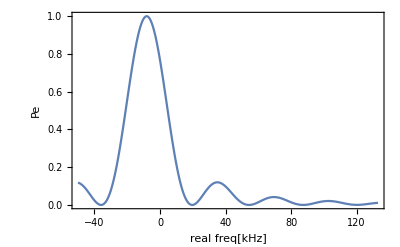

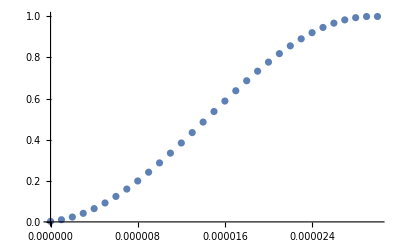

Ω0/2πkHz | t/us
11.57 | 30

n1 | n2 | cn1 | cn2
0 | 1 | 0 | 1

```mathematica
(*take spectrum*)
Clear[δ]
sim=Reap[
Do[
ρ1=ρ0;
Do[
k1=Δt f[ρ1,δ];
k2=Δt f[ρ1+k1/2,δ];
k3=Δt f[ρ1+k2/2,δ];
k4=Δt f[ρ1+k3,δ];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2),
{i,0,Ceiling[tEnd/Δt]}
]
Sow[{δ/(2π kHz),ρ1[[1,1]]+ρ1[[3,3]]}]
,{δ,-2π 50kHz,2π 133kHz,2π .3kHz}
]
][[2,1]];

ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}},Axes->False,Frame->True,FrameLabel->{"real freq[kHz]","Pe"},LabelStyle->{Black,17}]
{{"Ω0/2πkHz","t/us"},{Ω0/(2π kHz),tEnd/us}}//TableForm
{{"n1","n2","cn1","cn2"},{ns[[1]],ns[[2]], cn1, cn2}}//TableForm
```

```mathematica
{{34.835873983739816,0.12389379145737467}-{-7.938516260162629,1.002630949575204}}
```

{{42.7744,-0.878737}}

```mathematica
-8.1kHz
```

## save ground state, lower rabi freq. larger int shift

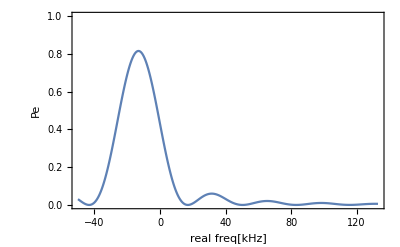

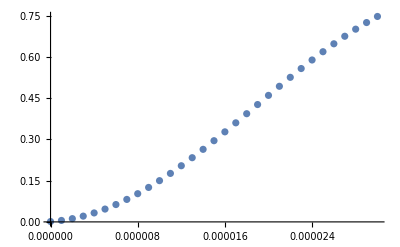

Ω0/2πkHz | t/us
11.57 | 30

n1 | n2 | cn1 | cn2
0 | 1 | 1 | 0

```mathematica
-13kHz
{{31.116361788617894,0.06601290080290667}-{-12.89786585365853,0.8342501767622066}}
```

{{44.0142,-0.768237}}

## save

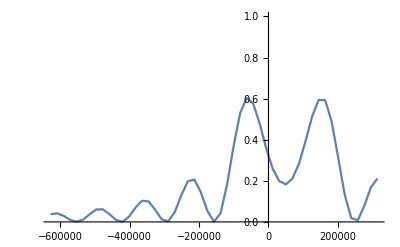

n1 | n2 | cn1 | cn2
0 | 4 | 0 | 1

## save

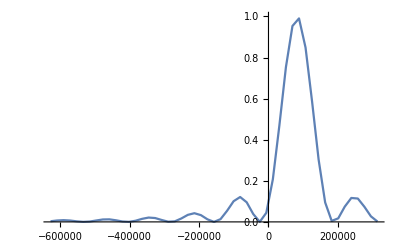

n1 | n2 | cn1 | cn2
0 | 4 | 1 | 0

## save

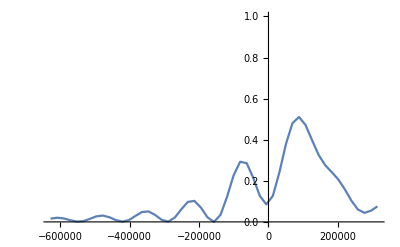

n1 | n2 | cn1 | cn2
0 | 3 | 0.707107 | 0.+0.707107 ⅈ

## save

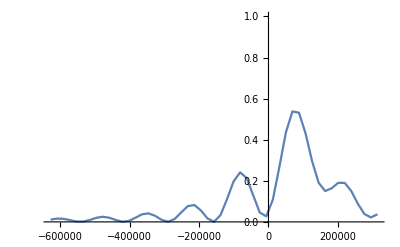

n1 | n2 | cn1 | cn2
0 | 2 | 0.707107 | 0.+0.707107 ⅈ

## save

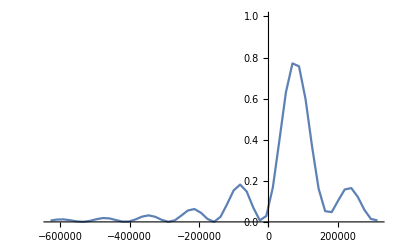

n1 | n2 | cn1 | cn2
0 | 1 | 0.707107 | 0.+0.707107 ⅈ

## w coherence

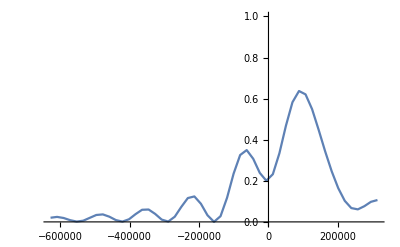

n1 | n2 | cn1 | cn2
0 | 4 | 0.707107 | 0.+0.707107 ⅈ

## coherences set to zero

-Graphics-

n1 | n2 | cn1 | cn2
0 | 4 | 0.707107 | 0.+0.707107 ⅈ

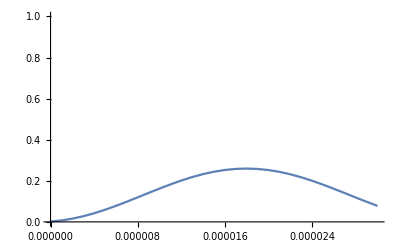

```mathematica
(*time evolve only*)
ρ1=ρ0;
sim=Reap[
Do[
δ=Ω0;

k1=Δt f[ρ1,δ];
k2=Δt f[ρ1+k1/2,δ];
k3=Δt f[ρ1+k2/2,δ];
k4=Δt f[ρ1+k3,δ];
ρ1=ρ1+1/3(k1/2+k2+k3+k4/2);
Sow[{Δt i,ρ1[[1,1]]+ρ1[[3,3]]}],
{i,0,Ceiling[tEnd/Δt]}
]
][[2,1]];
ListPlot[Chop[sim],Joined->True,PlotRange->{All,{0,1}}]
```